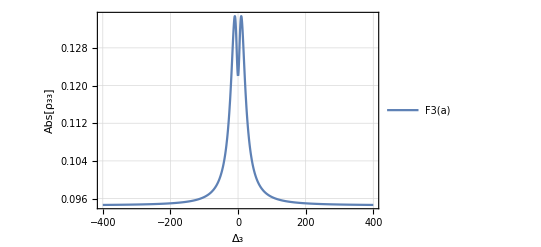

```mathematica
Subscript[Γ, 3]=13.4;
Subscript[Δ, 2]=0;
Subscript[Ω, p] =10.1;
Subscript[Ω, c]=10.1;
Subscript[γ, 1]=0.11;
Subscript[γ, 3]=2.4;
ℏ=1;
Subscript[Γ, 12]=7.0;H=-ℏ/2*{{0,0,Subscript[Ω, p]*Exp[-ⅈ*a*t]},{0,0,Subscript[Ω, c]*Exp[-ⅈ*Subscript[Δ, 2]*t]},{Subscript[Ω, p]*Exp[ⅈ*a*t],Subscript[Ω, c]*Exp[ⅈ*Subscript[Δ, 2]*t],0}};densitymatrix={{Subscript[ρ, 11],Subscript[ρ, 12],Subscript[ρ, 13]},{Subscript[ρ, 21],Subscript[ρ, 22],Subscript[ρ, 23]},{Subscript[ρ, 31],Subscript[ρ, 32],Subscript[ρ, 33]}};U={{1,0,0},{0,Exp[ⅈ*(a-Subscript[Δ, 2])*t],0},{0,0,Exp[ⅈ*a*t]}};NewH=Simplify[Conjugate[U].H.U-ⅈ*Conjugate[U].D[U,t],Element[t,Reals]&&Element[a,Reals]&&Element[Subscript[Δ, 2],Reals]];sigma13={{0,0,1},{0,0,0},{0,0,0}};sigma31={{0,0,0},{0,0,0},{1,0,0}};sigma33={{0,0,0},{0,0,0},{0,0,1}};sigma23={{0,0,0},{0,0,1},{0,0,0}};sigma32={{0,0,0},{0,0,0},{0,1,0}};sigma22={{0,0,0},{0,1,0},{0,0,0}};sigma12={{0,1,0},{0,0,0},{0,0,0}};sigma21={{0,0,0},{1,0,0},{0,0,0}};sigma11={{1,0,0},{0,0,0},{0,0,0}};L={{Subscript[Γ, 12]*(Subscript[ρ, 22]-Subscript[ρ, 11])+Subscript[Γ, 3]/2*Subscript[ρ, 33],-(Subscript[Γ, 12]+Subscript[γ, 1])*Subscript[ρ, 12],-(Subscript[Γ, 12]/2+Subscript[Γ, 3]/2+Subscript[γ, 3])*Subscript[ρ, 13]},{-(Subscript[Γ, 12]+Subscript[γ, 1])*Subscript[ρ, 21],Subscript[Γ, 12]*(Subscript[ρ, 11]-Subscript[ρ, 22])+Subscript[Γ, 3]/2*Subscript[ρ, 33],-(Subscript[Γ, 12]/2+Subscript[Γ, 3]/2+Subscript[γ, 3])*Subscript[ρ, 23]},{-(Subscript[Γ, 12]/2+Subscript[Γ, 3]/2+Subscript[γ, 3])*Subscript[ρ, 31],-(Subscript[Γ, 12]/2+Subscript[Γ, 3]/2+Subscript[γ, 3])*Subscript[ρ, 32],-Subscript[Γ, 3]*Subscript[ρ, 33]}};M=Simplify[-ⅈ*(NewH.densitymatrix-densitymatrix.NewH)+L,Element[t,Reals]&&Element[a,Reals]&&Element[Subscript[Δ, 2],Reals]];M[[1,1]]=Subscript[ρ, 11]+Subscript[ρ, 22]+Subscript[ρ, 33]-1;F1[a_]:=-Im[Subscript[ρ, 13]/.Solve[{M[[1,1]]==0,M[[1,2]]==0,M[[1,3]]==0,M[[2,1]]==0,M[[2,2]]==0,M[[2,3]]==0,M[[3,1]]==0,M[[3,2]]==0,M[[3,3]]==0},{Subscript[ρ, 11],Subscript[ρ, 12],Subscript[ρ, 13],Subscript[ρ, 21],Subscript[ρ, 22],Subscript[ρ, 23],Subscript[ρ, 31],Subscript[ρ, 32],Subscript[ρ, 33]}]][[1]];
F2[a_]:=-Im[Subscript[ρ, 23]/.Solve[{M[[1,1]]==0,M[[1,2]]==0,M[[1,3]]==0,M[[2,1]]==0,M[[2,2]]==0,M[[2,3]]==0,M[[3,1]]==0,M[[3,2]]==0,M[[3,3]]==0},{Subscript[ρ, 11],Subscript[ρ, 12],Subscript[ρ, 13],Subscript[ρ, 21],Subscript[ρ, 22],Subscript[ρ, 23],Subscript[ρ, 31],Subscript[ρ, 32],Subscript[ρ, 33]}]][[1]];F3[a_]:=Abs[Subscript[ρ, 33]/.Solve[{M[[1,1]]==0,M[[1,2]]==0,M[[1,3]]==0,M[[2,1]]==0,M[[2,2]]==0,M[[2,3]]==0,M[[3,1]]==0,M[[3,2]]==0,M[[3,3]]==0},{Subscript[ρ, 11],Subscript[ρ, 12],Subscript[ρ, 13],Subscript[ρ, 21],Subscript[ρ, 22],Subscript[ρ, 23],Subscript[ρ, 31],Subscript[ρ, 32],Subscript[ρ, 33]}]][[1]];
(*Plot[F1[a],{a,-400,350},PlotRange->All,AxesLabel->{Subscript[Δ, 1],-Im[Subscript[ρ, 12]]}, AxesOrigin->{-400,0}]
Plot[F2[a],{a,-400,350},PlotRange->All,AxesLabel->{Subscript[Δ, 2],-Im[Subscript[ρ, 23]]}, AxesOrigin->{-400,0}]*)
Plot[F3[a],{a,-400,400},PlotTheme->"Detailed",PlotRange->All,AxesLabel->{Subscript[Δ, 3],Abs[Subscript[ρ, 33]]}, AxesOrigin->{-400,0}]
```

```mathematica
H=-ℏ/2*{{0,0,Subscript[Ω, p]*Exp[-ⅈ*Subscript[Δ, 1]*t]},{0,0,Subscript[Ω, c]*Exp[-ⅈ*Subscript[Δ, 2]*t]},{Subscript[Ω, p]*Exp[ⅈ*Subscript[Δ, 1]*t],Subscript[Ω, c]*Exp[ⅈ*Subscript[Δ, 2]*t],0}};densitymatrix={{Subscript[ρ, 11],Subscript[ρ, 12],Subscript[ρ, 13]},{Subscript[ρ, 21],Subscript[ρ, 22],Subscript[ρ, 23]},{Subscript[ρ, 31],Subscript[ρ, 32],Subscript[ρ, 33]}};U={{1,0,0},{0,Exp[ⅈ*(Subscript[Δ, 1]-Subscript[Δ, 2])*t],0},{0,0,Exp[ⅈ*Subscript[Δ, 1]*t]}};NewH=Simplify[Conjugate[U].H.U-ⅈ*Conjugate[U].D[U,t],Element[t,Reals]&&Element[Subscript[Δ, 1],Reals]&&Element[Subscript[Δ, 2],Reals]];
```

```mathematica
NewH
```

{{0,0,-(ℏ Ω_p)/2},{0,Δ_1-Δ_2,-(ℏ Ω_c)/2},{-(ℏ Ω_p)/2,-(ℏ Ω_c)/2,Δ_1}}